a+(-ⅇ^-a-ⅇ^a+ⅇ^-x+ⅇ^x)/(-ⅇ^-a+ⅇ^a)-x

c+x

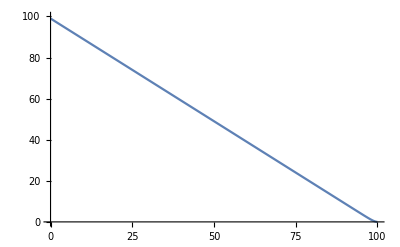

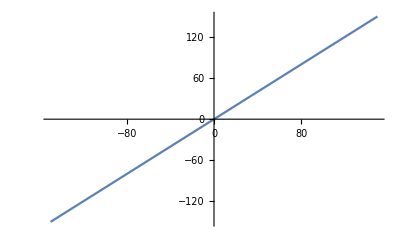

```mathematica
h1[x_,a_]= ((Tan[45Degree]*(E^x-E^a+E^(-x)-E^(-a)))/(E^(a)-E^(-a)))+Tan[45Degree]*(a-x)
h2[x_, b_, c_] =Tan[45Degree]*x+c
Plot[h1[x, 100],{x,0,100}, PlotRange->{0,100}]
Plot[h2[x, 100, 0],{x,-150,150}, PlotRange->{-150,150}]
Manipulate[
Plot[h1[x,a],{x,0,a}, PlotRange->a],
{a,100,1000}]
Manipulate[
Plot[h2[x,b,0],{x,-b,b}, PlotRange->b],
{b,100,1000}]
```